BookChapterNumber

Kosterlitz-Thouless Transition

## Spin Waves (Non-Topological Excitation)

When θ at each spin is close to θ of its neighbors, the Hamiltonian can be approximated by expanding the cosine terms (remove the constant terms):

H=1/2 J∑_⟨i,j⟩ (θ_i-θ_j)^2

On a Bravais lattice (counter examples include graphene), we rewrite the Hamiltonian as

H=1/4 J∑_(R,δ) (θ_R-θ_(R+δ))^2

where δ are the vectors to nearest neighbors. The additional 1/2 factor accounts for double counting, since since bond is shared by two sites. Perform Fourier transform

θ_R=1/N∑_k φ_k ⅇ^(ⅈ k R)

We note that since θ_R is a real number, we must have

θ_R*=1/N∑_k φ_k*ⅇ^(-ⅈ k R)=1/N∑_k φ_-k ⅇ^(-ⅈ k R)=θ_R

thus

φ_-k=φ_k*

Then

H=J/(4 N^2)∑_(R,δ) (∑_k φ_k ⅇ^(ⅈ k R)(1-ⅇ^(ⅈ k δ)))(∑_k' φ_k' ⅇ^(ⅈ k' R)(1-ⅇ^(ⅈ k' δ)))
=J/(4 N^2)∑_(R,δ) ∑_(k,k') (φ_k φ_k'(1-ⅇ^(ⅈ k δ))(1-ⅇ^(ⅈ k' δ))ⅇ^(ⅈ (k+k')R))

Summation over R gives a factor N δ_(k,-k'). Then

H=J/(4N)∑_(k,δ) (φ_k φ_-k(1-ⅇ^(ⅈ k δ))(1-ⅇ^(-ⅈ k δ)))
=1/N∑_k E(k)φ_k φ_-k=1/N∑_k E(k)(|φ_k|)^2

where the dispersion relation is

E(k)≡∑_δ J/4(1-ⅇ^(ⅈ k δ))(1-ⅇ^(-ⅈ k δ))=∑_δ J/2 (1-cos(k δ))

### Examples

#### Square Lattice

On a square lattice

δ=(a,0), (0,a), (-a,0), (0,-a)

Then

E(k)=J(2-cos(k_x a)-cos(k_y a))

For small k we can expand E(k) (using cos x≃1-x^2/2) as

E(k)=1/2 J a^2 k^2

the same as a harmonic oscillator.

#### Bravais Lattice with A Basis (e.g. Graphene / Honeycomb)

-Graphics-

Honeycomb lattice is special because it is composed of two triangular sub-lattices (call them A and B). For sub-lattice A,

δ_1≡(0,1)a, δ_2≡((√3)/2,-1/2)a, δ_3≡(-(√3)/2,-1/2)a

For sub-lattice B

δ_l^B=-δ_l^A

We perform Fourier transform on A and B sub-lattices separately:

θ_R=1/N∑_k a_k ⅇ^(ⅈ k R)  (R∈A), θ_R=1/N∑_k b_k ⅇ^(ⅈ k R)  (R∈B)

with the requirement

a_-k=a_k*,  b_-k=b_k*

Then

H=1/4 J∑_(R∈A,δ) (θ_R-θ_(R+δ))^2+1/4 J∑_(R∈B,δ) (θ_R-θ_(R-δ))^2
=J/(4 N^2)[∑_(R∈A,δ) ∑_(k,k') (a_k ⅇ^(ⅈ k R)-b_k ⅇ^(ⅈ k (R+δ)))(a_k' ⅇ^(ⅈ k' R)-b_k' ⅇ^(ⅈ k' (R+δ)))
	+∑_(R∈B,δ) ∑_(k,k') (b_k ⅇ^(ⅈ k R)-a_k ⅇ^(ⅈ k (R-δ)))(b_k' ⅇ^(ⅈ k' R)-a_k' ⅇ^(ⅈ k' (R-δ)))]
=J/(4 N^2)[∑_(R∈A,δ) ∑_(k,k') (a_k a_k'-a_k b_k' ⅇ^(ⅈ k' δ)-b_k a_k' ⅇ^(ⅈ k δ)+b_k b_k' ⅇ^(ⅈ (k+k')δ))ⅇ^(ⅈ(k+k')R)
	+∑_(R∈B,δ) ∑_(k,k') (b_k b_k'-b_k a_k' ⅇ^(-ⅈ k' δ)-a_k b_k' ⅇ^(-ⅈ k δ)+a_k a_k' ⅇ^(ⅈ(k+k')δ))ⅇ^(ⅈ(k+k')R)]

The two summations over R∈A (or B) gives N δ_(k,-k'). This cancels one N in the denominator, and set k=-k'. Renaming k' to k, we obtain

H=J/(4N)[∑_(k,δ) (a_-k a_k-a_-k b_k ⅇ^(ⅈ k δ)-b_-k a_k ⅇ^(-ⅈ k δ)+b_-k b_k)
	+∑_(k,δ) (b_-k b_k-b_-k a_k ⅇ^(-ⅈ k δ)-a_-k b_k ⅇ^(ⅈ k δ)+a_-k a_k)]
=J/(2N)[∑_(k,δ) (a_k*a_k-a_k*b_k ⅇ^(ⅈ k δ)-b_k*a_k ⅇ^(-ⅈ k δ)+b_k*b_k)]
=1/N∑_k (a_k* | b_k*)J/2(3 | -∑_δ ⅇ^(ⅈ k δ)
-∑_δ ⅇ^(-ⅈ k δ) | 3)(a_k
b_k)

The Bloch Hamiltonian is then

H(k)=J/2(3 | -∑_δ ⅇ^(ⅈ k δ)
-∑_δ ⅇ^(-ⅈ k δ) | 3)

Thus there will be two dispersion relations, which are eigenvalues of H(k):

E_±(k)=J/2(3±√(3+2cos(√3 k_x a)+4cos((√3)/2 k_x a)cos(3/2 k_y a)))

visualized below (with J=1,a=1)

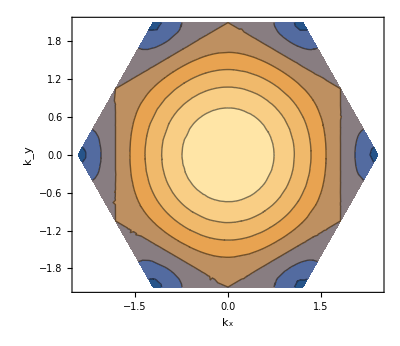

```mathematica
Clear["Global`*"]
b={{2π,(2π)/(√3)},{-2π,(2π)/(√3)}}/√3;
Κ={(4π)/3,0}/√3;Κ′={(2π)/3,(2π)/(√3)}/√3;
BZ=Polygon[{Κ,Κ′,Κ+b[[2]],-Κ,-Κ′,Κ′-b[[1]]-b[[2]]}];
ContourPlot[1/2(3+√(3+2Cos[√3 kx]+4Cos[(√3)/2 kx]Cos[3/2 ky])),{kx,ky}∈BZ,FrameStyle->White,FrameLabel->{"k_x","k_y"},AspectRatio->√3/2]
```

## Correlation Function

By definition g(x_i-x_j)=⟨(s_i-(s̄)_i)·(s_j-(s̄)_j)⟩. But it can be shown that (s̄)_i=0 at finite temperature, thus we only need to calculate

G(x_i)≡⟨s_i·s_0⟩=⟨cos(θ_i-θ_0)⟩

We play the trick

G(x_i)=Re ⟨exp[ⅈ(θ_i-θ_0)]⟩ (⟶_fluctuation)^Gaussian exp(-1/2⟨(θ_i-θ_0)^2⟩)

Then we use Fourier transform to evaluate

θ_R=1/N∑_k φ_k ⅇ^(ⅈ k R)

⟨(θ_i-θ_0)^2⟩=⟨1/N^2∑_(k,k') (φ_k ⅇ^(ⅈ k R_i)-φ_k)(φ_k' ⅇ^(ⅈ k' R_i)-φ_k')⟩
=1/N^2∑_(k,k') ⟨φ_k φ_k'⟩(ⅇ^(ⅈ(k+k')R_i)-ⅇ^(ⅈ k R_i)-ⅇ^(ⅈ k' R_i)+1)

We can show that (see appendix)

⟨φ_k φ_k'⟩=(N T)/(E(k))δ_(k',-k)

Thus

⟨(θ_i-θ_0)^2⟩=1/N∑_k T/(E(k))(2-ⅇ^(ⅈ k R_i)-ⅇ^(-ⅈ k R_i))
=1/N∑_k (2T)/(E(k))(1-cos(k R_i)) ⟶^(E(k)=1/2 J a^2 k^2) (4T)/(J a^2)1/N∑_k (1-cos(k R_i))/k^2

Take the continuum limit

ⅆ k_i=(2π)/(N a) ⟹ 1/N∑_k ⟶ (a/(2π))^d∫ⅆ^d k

We obtain (correct in any spatial dimension d)

⟨(θ_i-θ_0)^2⟩=(4T a^(d-2))/J∫(ⅆ^d k)/(2π)^d(1-cos(k R_i))/k^2

## Topological Invariant (Charge)

Now consider the continuum limit of the model.

H≃1/2 J∑_⟨i,j⟩ (θ_i-θ_j)^2→1/2 J∫ⅆ^2 x (∇θ(x))^2

Consider a closed loop C on the lattice. Let the angle difference between the ith site and the (i+1)th site be δ θ_i. The topological invariant (winding number) is

γ_C=∑_C δ θ_i ⟶^continuum∮_C ∇θ(x)·ⅆl

After going through this loop, θ should return to its original value up to a change of 2π Q, with Q∈ℤ. Thus

γ_C=2π Q

This property guarantees that γ_C is invariant under a small change of the θ configuration.

A nonzero Q means that there are vortices (or anti-vortices) enclosed in the loop C. Otherwise (Q=0), there are only spin waves.

## Analogy with 2D Coulomb Gas

### Configuration Energy

Here we consider the continuum limit. The field θ(x) can be separated into two parts:

θ=ψ+φ

where ψ is curl-less (potential), describing spin waves:

∇×(∇ψ)=0 ⟹ ∮ ∇ψ·ⅆl=0

and φ is sourceless (divergence-less), describing vortices:

∇·(∇φ)=0,  ∇×(∇φ)≡2π ρ(x) e_z

⟹ ∮_C (∇φ)·ⅆl=∫_S ∇×(∇φ)·nⅆS=2π∫_S ρ(x)ⅆ^2 x=2π Q

S in the area enclosed in the loop C. Thus ρ(x) defined here is the surface density of the topological charge.

We note that the gradient of φ will appear frequently below. Let us give it a new name

V≡∇φ

Since φ is sourceless, ∇φ cannot have normal components at the boundary. Thus the boundary condition for V is

n·V=0

The energy of the system

H=J/2∫ⅆ^2 x (∇ψ+∇φ)^2=J/2∫ⅆ^2 x ((∇ψ)^2+(∇φ)^2+2∇ψ·∇φ)

But

J∫ⅆ^2 x∇ψ·∇φ=J∫ⅆ^2 x ∇·(ψ∇φ)-J∫ⅆ^2 x ψ(∇^2 φ)_(=0)
=J∮_boundary ψ (∇φ·n)_(=0)ⅆl=0

Thus H is separated into a ψ-term and a φ-term:

H=(J/2∫ⅆ^2 x (∇ψ)^2)_(spin wave)+(J/2∫ⅆ^2 x (∇φ)^2)_vortex

### Analogy with Electrostatics

The vortex energy

H=J/2∫ⅆ^2 x V^2

Recall that

∇×V=2π ρ ⅇ_z ⟹ e_z·(∇×V)=∇·(-e_z×V)=2π ρ

which is similar to the electrostatic equation (SI unit)

∇·E=ρ/ϵ_0

Thus, we define

E=-e_z×V=(V_y,-V_x,0)  ⟹  ∇·E=2π ρ

Applying results from electrostatics, we find the system energy

H=ϵ_0/2∫ⅆ^2 x E→

## Appendix: Finding ⟨φ_k φ_k'⟩

By definition

⟨φ_k φ_k'⟩=Tr[ⅇ^(-β H)φ_k φ_k']/Tr[ⅇ^(-β H)]=

Here the trace means a summation over all configurations of {φ_k}:

Tr[f]=∫∏_p ⅆ φ_pf≡∫[ⅆ φ_k]f

Then (note that E(k)=E(-k))

Tr[ⅇ^(-β H)φ_k φ_k']=∫[∏_p ⅆ φ_p] exp(-β/N∑_p E(p)φ_p φ_-p)φ_k φ_k'
=∫[∏_(p≠±k,±k') ⅆ φ_p] exp(-β/N∑_(p≠±k,±k') E(p)φ_p φ_-p)
	×(∫ⅆ φ_kⅆ φ_-kⅆ φ_k'ⅆ φ_-k' φ_k φ_k' exp(-β/N∑_(p=±k,±k') E(p)φ_p φ_-p))_(≡ I)

When k'=±k, the integration is easy:

1. k'=k

I=∫ⅆ φ_kⅆ φ_-k φ_k^2 exp((-2β)/N E(k)φ_k φ_-k)

Note that

∂/(∂(β E(k)))ln[Tr[ⅇ^(-β H)]]=1/Tr[ⅇ^(-β H)]∂/(∂(β E(k)))Tr[ⅇ^(-β H)]
=1/Tr[ⅇ^(-β H)]Tr[∂/(∂(β E(k)))ⅇ^(-β H)]
=1/Tr[ⅇ^(-β H)]Tr[∂/(∂(β E(k)))exp(-1/N∑_p β E(p)φ_p φ_-p)]
=1/Tr[ⅇ^(-β H)]Tr[-1/N φ_k φ_-k exp(-β H)]=-1/N⟨φ_k φ_-k⟩

Thus

⟨φ_k φ_-k⟩=-N∂/(∂(β E(k)))ln[Tr[ⅇ^(-β H)]]

```mathematica
int1=Simplify[∫r^(3-4t)ⅆr]
int2=Simplify[∫r^(1-4t)ⅆr]
```

r^(4-4 t)/(4-4 t)

r^(2-4 t)/(2-4 t)

```mathematica
FullSimplify[((int1/.{r->L})-(int1/.{r->a}))/((int2/.{r->L})-(int2/.{r->a}))//Expand,{L>0&&a>0&&t>1}]
```

((-a^(4 t) L^4+a^4 L^(4 t)) (-1+2 t))/(2 (-a^(4 t) L^2+a^2 L^(4 t)) (-1+t))